```mathematica
poly:={{{0,0},{3,0},{3,3}},{{1,0},{1,3},{4,0}},{{1,4},{2,5},{3,4}},{{1,2},{1,4},{3,4},{3,2}}}
```

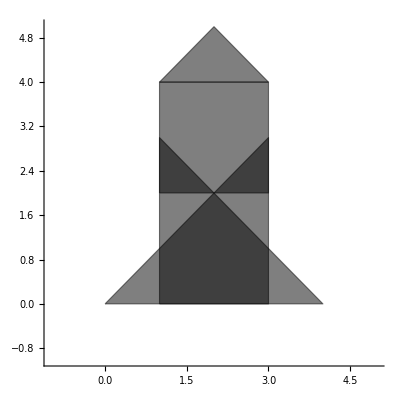

```mathematica
Graphics[{EdgeForm[Directive[Thick,Dashed,c]],Opacity[.5],{Polygon[Append[#,First[#]]] & /@ poly}},Axes->True,PlotRange->{{-1,5},{-1,5}}]
```

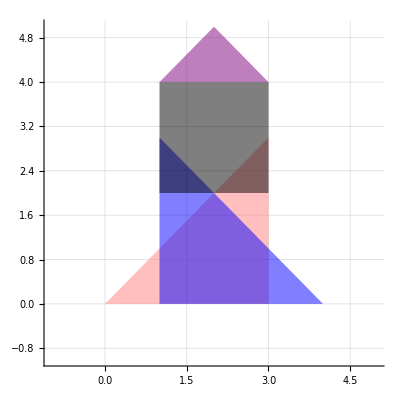

```mathematica
Show[Graphics[{EdgeForm[],Opacity[.5],Pink,Polygon[{{0,0},{3,0},{3,3}}]},GridLines->Automatic,GridLinesStyle->Directive[Dashed, LightGray]],
Graphics[{EdgeForm[],Opacity[.5],Blue,Polygon[{{1,0},{1,3},{4,0}}]}],
Graphics[{EdgeForm[],Opacity[.5],Purple,Polygon[{{1,4},{2,5},{3,4}}]}],
Graphics[{EdgeForm[],Opacity[.5],Black,Polygon[{{1,2},{1,4},{3,4},{3,2}}]}],PlotRange->{{-1,5},{-1,5}},Axes->True]
```

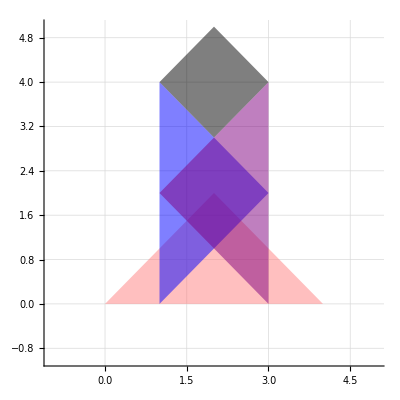

```mathematica
Show[Graphics[{EdgeForm[],Opacity[.5],Pink,Polygon[{{0,0},{4,0},{2,2}}]},GridLines->Automatic,GridLinesStyle->Directive[Dashed, LightGray]],
Graphics[{EdgeForm[],Opacity[.5],Blue,Polygon[{{1,0},{1,4},{3,2}}]}],
Graphics[{EdgeForm[],Opacity[.5],Purple,Polygon[{{3,0},{3,4},{1,2}}]}],
Graphics[{EdgeForm[],Opacity[.5],Black,Polygon[{{1,4},{2,5},{3,4},{2,3}}]}],PlotRange->{{-1,5},{-1,5}},Axes->True]
```

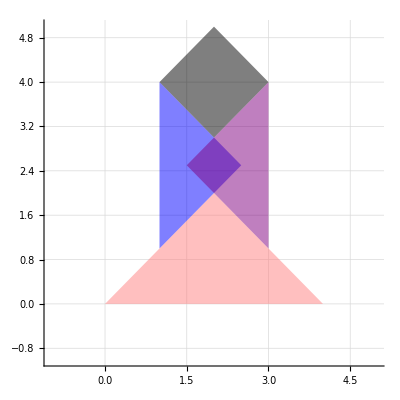

```mathematica
Show[Graphics[{EdgeForm[],Opacity[.5],Pink,Polygon[{{0,0},{4,0},{2,2}}]},GridLines->Automatic,GridLinesStyle->Directive[Dashed, LightGray]],
Graphics[{EdgeForm[],Opacity[.5],Blue,Polygon[{{1,1},{1,4},{2.5,2.5}}]}],
Graphics[{EdgeForm[],Opacity[.5],Purple,Polygon[{{3,1},{3,4},{1.5,2.5}}]}],
Graphics[{EdgeForm[],Opacity[.5],Black,Polygon[{{1,4},{2,5},{3,4},{2,3}}]}],PlotRange->{{-1,5},{-1,5}},Axes->True]
```